```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/software/Smoldyn/trunk/examples/S99_more/antigen

```mathematica
simdata=Import["antigenout.txt","CSV"];
```

```mathematica
time=simdata[[All,1]];
```

```mathematica
a=Transpose[{time,simdata[[All,2]]}];
ar=Transpose[{time,simdata[[All,3]]}];
arr=Transpose[{time,simdata[[All,4]]}];
arrr=Transpose[{time,simdata[[All,5]]}];
```

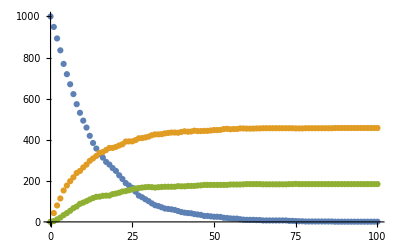

```mathematica
ListPlot[{ar,arr,arrr}]
```